Kitaev Random Circuit |

Remarkspaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#2005240608 | Analysispaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#1487900726
Setting up the modelpaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#516853239 | Direct Simulation for Green’s Functionspaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#286700255
Simulationpaclet:QuantumPlaybook/tutorial/KitaevRandomCircuit#1068023573 |

Here, the effects of random measurements on the entanglement in the Kitaev chain of Majorana fermions is investigated. A realization of such Kitaev random circuit is shown in Figure 1.

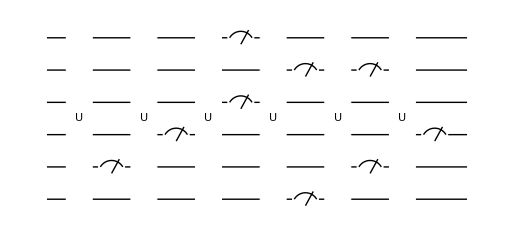

Figure 1. A typical form of Kitaev random circuit. Each line indicates a fermion mode, the unitary gate with label U denotes the time-evolution of Kitaev's model of Majorana fermions, and the measurement symbols depict the measurement of occupation number of the fermion modes.

WickStatepaclet:Q3/ref/WickStateQ3 Package Symbol | Represents a Wick state
WickUnitarypaclet:Q3/ref/WickUnitaryQ3 Package Symbol | A Bogoliubov-de Gennes-type transformation representing a time-evolution of fermionic system
NambuMatrixpaclet:Q3/ref/NambuMatrixQ3 Package Symbol | Matrix in the Nambu space
WickCircuitpaclet:Q3/ref/WickCircuitQ3 Package Symbol | Quantum circuit consisting of fermionic gates such as WickUnitarypaclet:Q3/ref/WickUnitaryQ3 Package Symbol and Measurementpaclet:Q3/ref/MeasurementQ3 Package Symbol[{c_1,c_2,…].
WickRandomCircuitpaclet:Q3/ref/WickRandomCircuitQ3 Package Symbol | Rancomd quantum circuit consisting of fermionic gates.
WickHistorypaclet:Q3/ref/WickHistoryQ3 Package Symbol | Reconstruct the history of the current Wick state.
WickGreensFunctionpaclet:Q3/ref/WickGreensFunctionQ3 Package Symbol | Calculates the Green's functions with respect to a Wick state
WickEntanglementEntropypaclet:Q3/ref/WickEntanglementEntropyQ3 Package Symbol | Calculates the entanglement entropy in a Wick state
WickLogarithmicNegativitypaclet:Q3/ref/WickLogarithmicNegativityQ3 Package Symbol | Calculates the logarithmic negativity in a Wick state

Functions for fermionic quantum computing.

Make sure to load Q3.

```mathematica
<<Q3`
```

This document requires the recent version of Q3.

```mathematica
Q3Assure["3.4.6"]
```

Remarks

By default (“Output”->”States”), the simulation returns (and saves if necessary) the trajectories of Wick states  (see WickRandomCircuit and  WickState for details). This is inefficient in terms of memory, but may be faster for data analysis. Moreover, this is better for physically understanding what is going on.

With option “Output”->”Correlations”, the simulation returns the trajectories of Green’s functions (see WickRandomCircuit and  WickGreensFunction for details). Since we are dealing with non-interacting models, the information of Green’s functions should be enough for most purposes. When you are only interested in a particular feature (for example, the entanglement entropy), the simulation itself takes unnecessarily longer.

Setting up the model

The bare fermion modes.

```mathematica
Let[Fermion,c]
```

Consider a system of n fermion modes.

```mathematica
$n=6;
cc=c[Range@$n]
cccc=Join[cc,Dagger@cc];
```

{c_(,,1),c_(,,2),c_(,,3),c_(,,4),c_(,,5),c_(,,6)}

Construct the many-body Hamiltonian of the Kitaev chain (Kitaev, 2001)https://doi.org/10.1070/1063-7869/44/10S/S29.

```mathematica
HH=-Q[cc]-t*PlusDagger[Hop@cc]+Δ*PlusDagger[Pair@cc]//Garner
```

-Graphics-

Examine the connectivity between neighboring fermion modes.

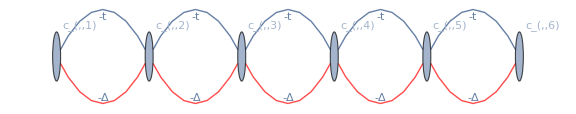

```mathematica
GraphForm[HH]
```

Extract the single-particle (or Bogoliubov-de Gennes) Hamiltonian (cf. many-body Hamiltonian in the above) of the model in the Nambu space.

```mathematica
barH=CoefficientTensor[HH,Dagger@cccc,cccc];
barH[[;;UpTo[8],;;UpTo[8]]]//MatrixForm
```

(-1/2 | -t/2 | 0 | 0 | 0 | 0 | 0 | -Δ/2
-t/2 | -1/2 | -t/2 | 0 | 0 | 0 | Δ/2 | 0
0 | -t/2 | -1/2 | -t/2 | 0 | 0 | 0 | Δ/2
0 | 0 | -t/2 | -1/2 | -t/2 | 0 | 0 | 0
0 | 0 | 0 | -t/2 | -1/2 | -t/2 | 0 | 0
0 | 0 | 0 | 0 | -t/2 | -1/2 | 0 | 0
0 | Δ/2 | 0 | 0 | 0 | 0 | 1/2 | t/2
-Δ/2 | 0 | Δ/2 | 0 | 0 | 0 | t/2 | 1/2)

The time interval for each unitary layer to operate.

```mathematica
$τ=0.5;
```

Construct the single-particle unitary matrix in the Nambu space. Recall the convention:
	c̲ ↦U̲ c̲  with (c̲)^†:=(c_1,…,c_n,c_1^†,…,c_n^†) and  U̲:=(U | V
V^* | U^*).

```mathematica
barU=MatrixExp[-I*$τ*Normal[barH]/.{t->1,Δ->1}];
barU[[;;UpTo[5],;;UpTo[5]]]//MatrixForm
```

(0.908981+0.237213 ⅈ | -0.0599369+0.232165 ⅈ | 0.000633605-0.00501574 ⅈ | -2.65865×10^-6+0.000031737 ⅈ | 5.95904×10^-9-9.50461×10^-8 ⅈ
-0.0599369+0.232165 ⅈ | 0.849041+0.22715 ⅈ | -0.0593032+0.232229 ⅈ | 0.000630946-0.00501593 ⅈ | -2.65269×10^-6+0.0000317374 ⅈ
0.000633605-0.00501574 ⅈ | -0.0593032+0.232229 ⅈ | 0.849039+0.227149 ⅈ | -0.0593032+0.232229 ⅈ | 0.000630946-0.00501593 ⅈ
-2.65865×10^-6+0.000031737 ⅈ | 0.000630946-0.00501593 ⅈ | -0.0593032+0.232229 ⅈ | 0.849039+0.227149 ⅈ | -0.0593032+0.232229 ⅈ
5.95904×10^-9-9.50461×10^-8 ⅈ | -2.65269×10^-6+0.0000317374 ⅈ | 0.000630946-0.00501593 ⅈ | -0.0593032+0.232229 ⅈ | 0.849041+0.22715 ⅈ)

Construct the corresponding unitary operator. It has the same information as the above unitary matrix, but operates directly on Wick states.

```mathematica
wu=WickUnitary[barU,cc]
```

WickUnitary[…]

The probability to perform a measurement on each fermion mode.

```mathematica
$p=.2;
```

The depth of quantum circuit.

```mathematica
$T=6; (* must be an integer *)
```

Simulation

The simulation involves a lot of random number generators. To get the same result every time you open this document, set the seed of the random number generator.

```mathematica
SeedRandom[344];(*for tests*)
```

Construct 10 random circuits and run each circuit 5 times. Notice the "Samples"→{10,5} option.

```mathematica
EchoTiming[
data=WickRandomCircuit[cc,wu,$p,$T,
"InitialOccupation"->PadRight[{1,1},$n],
"Samples"->{10,5}];
]
```

1.61273

Examine the output data format: There are 10 entries because the same number of quantum circuits were randomly generated.

```mathematica
Length[data]
```

10

Each entry is a pair {circuit_i,{out_i1,out_i2,…}} of quantum circuit circuit_i and a list of output states out_ij from circuit_i.

```mathematica
data[[2]]
```

{WickCircuit[…],{WickState[…],WickState[…],WickState[…],WickState[…],WickState[…]}}

If you want, examine the circuits by displaying them in a graphical form.

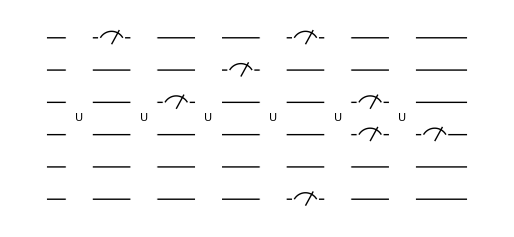

```mathematica
Show[data[[2,1]]]
```

Examine some of the output states as well.

```mathematica
out=data[[2,2,3]]
```

WickState[…]

```mathematica
Elaborate[out]
```

(0.0018158+0.00251524 ⅈ) 0_(,,c_(,,1))0_(,,c_(,,2))0_(,,c_(,,3))1_(,,c_(,,4))0_(,,c_(,,5))1_(,,c_(,,6))+(0.00464515-0.00324142 ⅈ) 0_(,,c_(,,1))0_(,,c_(,,2))0_(,,c_(,,3))1_(,,c_(,,4))1_(,,c_(,,5))0_(,,c_(,,6))-(0.00688881+0.00779569 ⅈ) 0_(,,c_(,,1))0_(,,c_(,,2))1_(,,c_(,,3))1_(,,c_(,,4))0_(,,c_(,,5))0_(,,c_(,,6))+(0.00516576-0.0009078 ⅈ) 0_(,,c_(,,1))0_(,,c_(,,2))1_(,,c_(,,3))1_(,,c_(,,4))1_(,,c_(,,5))1_(,,c_(,,6))-(0.0305964-0.0274095 ⅈ) 0_(,,c_(,,1))1_(,,c_(,,2))0_(,,c_(,,3))1_(,,c_(,,4))0_(,,c_(,,5))0_(,,c_(,,6))-(0.00376075+0.0206544 ⅈ) 0_(,,c_(,,1))1_(,,c_(,,2))0_(,,c_(,,3))1_(,,c_(,,4))1_(,,c_(,,5))1_(,,c_(,,6))-(0.000407692-0.00174713 ⅈ) 0_(,,c_(,,1))1_(,,c_(,,2))1_(,,c_(,,3))1_(,,c_(,,4))0_(,,c_(,,5))1_(,,c_(,,6))+(0.00295888-0.000132742 ⅈ) 0_(,,c_(,,1))1_(,,c_(,,2))1_(,,c_(,,3))1_(,,c_(,,4))1_(,,c_(,,5))0_(,,c_(,,6))+(0.0507813+0.0557227 ⅈ) 1_(,,c_(,,1))0_(,,c_(,,2))0_(,,c_(,,3))1_(,,c_(,,4))0_(,,c_(,,5))0_(,,c_(,,6))-(0.0378475-0.00721493 ⅈ) 1_(,,c_(,,1))0_(,,c_(,,2))0_(,,c_(,,3))1_(,,c_(,,4))1_(,,c_(,,5))1_(,,c_(,,6))+(0.00283719+0.000934332 ⅈ) 1_(,,c_(,,1))0_(,,c_(,,2))1_(,,c_(,,3))1_(,,c_(,,4))0_(,,c_(,,5))1_(,,c_(,,6))+(0.0000832873-0.00476922 ⅈ) 1_(,,c_(,,1))0_(,,c_(,,2))1_(,,c_(,,3))1_(,,c_(,,4))1_(,,c_(,,5))0_(,,c_(,,6))+(0.00608725-0.000812092 ⅈ) 1_(,,c_(,,1))1_(,,c_(,,2))0_(,,c_(,,3))1_(,,c_(,,4))0_(,,c_(,,5))1_(,,c_(,,6))-(0.0014345+0.0111144 ⅈ) 1_(,,c_(,,1))1_(,,c_(,,2))0_(,,c_(,,3))1_(,,c_(,,4))1_(,,c_(,,5))0_(,,c_(,,6))-(0.0167142-0.00936507 ⅈ) 1_(,,c_(,,1))1_(,,c_(,,2))1_(,,c_(,,3))1_(,,c_(,,4))0_(,,c_(,,5))0_(,,c_(,,6))+(0.000341495-0.00965495 ⅈ) 1_(,,c_(,,1))1_(,,c_(,,2))1_(,,c_(,,3))1_(,,c_(,,4))1_(,,c_(,,5))1_(,,c_(,,6))

The above output data is memory efficient, but may not be convenient for analysis. Convert it to the list of pairs {wc_k,ws_k} of Wick circuit wc_k and output Wick state ws_k.

```mathematica
wcs=Catenate[Thread/@data];
```

There are 50 entries; (10 circuits)×(5 output states per each circuit)

```mathematica
Dimensions[wcs]
```

{50,2}

```mathematica
wcs[[2]]
```

{WickCircuit[…],WickState[…]}

Analysis

Each entry in the converted data wcs contains the information about one realization of quantum trajectory. Extract the trajectory history in an explicit form, for example, of the first entry.

```mathematica
trj=WickHistory[First@wcs]
```

{WickState[…],WickState[…],WickState[…],WickState[…],WickState[…],WickState[…],WickState[…],WickState[…],WickState[…],WickState[…],WickState[…],WickState[…],WickState[…]}

In this particular case, there are 13 entries; the first entry is just the initial state and the rest are corresponds to the layers; there are 6 layers and each layer contains two sublayers of unitary evolution and measurements.

```mathematica
Dimensions[trj]
```

{13}

For further analysis, take the subsystem. Below, we will consider entanglement properties between this subsystem and the rest.

```mathematica
aa=Take[cc,Floor[$n/2]]
```

{c_(,,1),c_(,,2),c_(,,3)}

### Logarithmic Negativity: simple example

For further analysis, take the subsystem. This has been defined above; just in case.

```mathematica
aa=Take[cc,Floor[$n/2]];
```

At the moment, the current implementation of WickLogarithmicNegativity does not handle trivial cases of Green’s function, which internally lead to singular matrices. To avoid such cases, put a small value to the “Epsilon” option.

```mathematica
SetOptions[WickLogarithmicNegativity,"Epsilon"->1.25*^-5]
```

{Epsilon→0.0000125}

Calculate the logarithmic negativity of each state in the particular trajectory.

```mathematica
EchoTiming@Quiet[
ent=WickLogarithmicNegativity[aa]/@trj;,
{Inverse::sing,Inverse::luc,Power::infy}
]
```

WickTimeReversalMoment::sing: The matrix is tamed according to option "Epsilon".

General::stop: Further output of WickTimeReversalMoment::sing will be suppressed during this calculation.

Det::luc: Result for Det of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of Det::luc will be suppressed during this calculation.

1.22959

Plot the entanglement (logarithmic negativity) of the first trajectory.

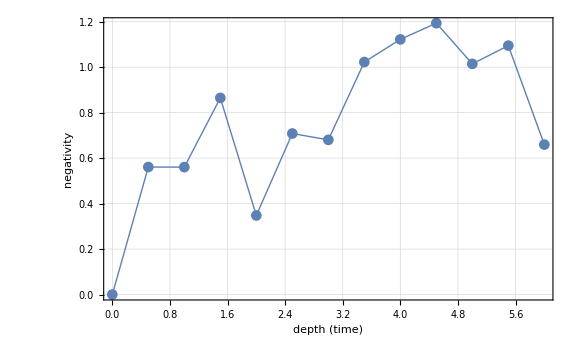

```mathematica
ListLinePlot[Re@ent,
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"depth (time)", "negativity"}]
```

### Entanglement Entropy: simple example

As another way to characterize the entanglement, calculate the entanglement entropy (note that each state in a given trajectory is a pure state).

For further analysis, take the subsystem. This has been defined above; just in case.

```mathematica
aa=Take[cc,Floor[$n/2]];
```

Calculate the entanglement entropy.

```mathematica
EchoTiming[ee=WickEntanglementEntropy[#,aa]&/@trj]
```

Det::luc: Result for Det of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of Det::luc will be suppressed during this calculation.

0.293968

{0,0.327406,0.327009,0.746187,0.134654,0.402829,0.471961,0.672045,0.933162,0.929062,0.769916,0.938647,0.332297}

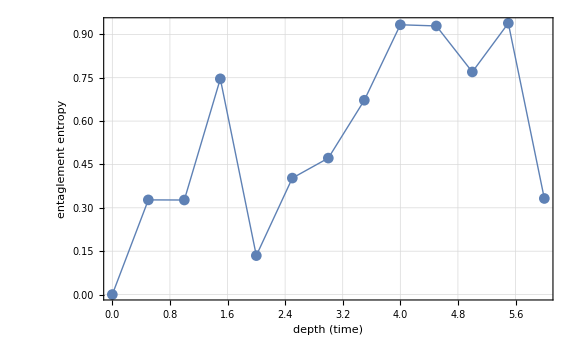

```mathematica
ListLinePlot[ee,
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"depth (time)", "entaglement entropy"}]
```

### Entanglement Entropy: more complete analysis

Let us now take all trajectories into account.

```mathematica
EchoTiming[trj=WickHistory/@wcs;]
```

0.082084

Recall that in this particular example, there are 50 trajectories; and 13 Wick states along each trajectory.

```mathematica
Dimensions[trj]
```

{50,13}

Again, the subsystem has a half of the whole modes.

```mathematica
aa=Take[cc,Floor[$n/2]]
```

{c_(,,1),c_(,,2),c_(,,3)}

Calculate the entanglement entropy.

```mathematica
EchoTiming[ee=Map[WickEntanglementEntropy[#,aa]&,trj,{2}];]
```

Det::luc: Result for Det of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of Det::luc will be suppressed during this calculation.

14.8631

Take the average of the entanglement entropy over different trajectories, and plot it as a function of time.

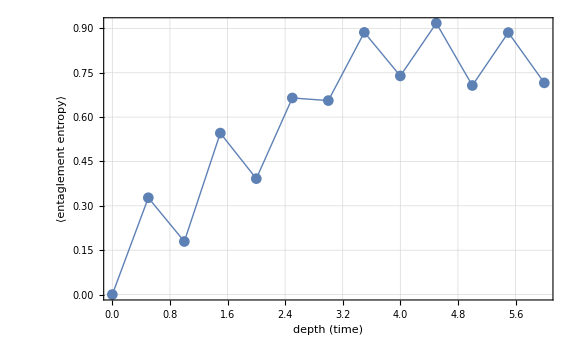

```mathematica
ListLinePlot[Mean[ee],
DataRange->{0,$T},
PlotMarkers->Automatic,
FrameLabel->{"depth (time)", "⟨entaglement entropy⟩"}]
```

Direct Simulation for Green’s Functions

The option “Output”->”Correlations” allows us to directly calculate the Green’s functions, with which most physical properties can be investigated for non-interacting models.

Again, set the seed of the random number generator.

```mathematica
SeedRandom[344];(*for tests*)
```

Construct 10 random circuits and run each circuit 2 times.

```mathematica
EchoTiming[
data=WickRandomCircuit[cc,wu,$p,$T,
"InitialOccupation"->PadRight[{1,1},$n],
"Samples"->{10,2},
"Output"->"Correlations"
];
]
```

Det::luc: Result for Det of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of Det::luc will be suppressed during this calculation.

21.6704

The simulation returns a two-dimensional array of pairs {G,F}, where G and F are the n×n matrices corresponding to the normal and anomalous Green’s functions, respectively, for n fermion modes.

In this particular example, there are 20 trajectories (10 random circuits and 2 random outputs from each circuit), and each trajectory consists of 13 states along the history of time evolution.

```mathematica
Dimensions[data]
```

{20,13}

Here is the second point on the 3rd trajectory.

```mathematica
data[[3,2]]
```

NambuMatrix[…]

Take the index of the fermion mode in the subsystem.

```mathematica
kk=Range@Floor[$n/2]
```

{1,2,3}

Calculate the entanglement entropy from each Green’s functions.

```mathematica
EchoTiming[ent=Map[WickEntanglementEntropy[#,kk]&,data,{2}];]
```

0.041058

Take the average of the entanglement entropy over different trajectories, and plot it as a function of time.

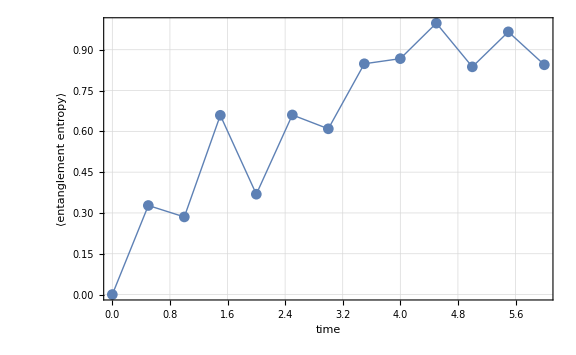

```mathematica
ListLinePlot[Mean[ent],
PlotMarkers->Automatic,
DataRange->{0,$T},
FrameLabel->{"time","⟨entanglement entropy⟩"}]
```

| Related Guides
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪B. M. Terhal and D. P. DiVincenzo (2002)https://doi.org/10.1103/PhysRevA.65.032325, Physical Review A 65, 032325, "Classical simulation of noninteracting-fermion quantum circuits."
▪A. Yu. Kitaev (2001)https://doi.org/10.1070/1063-7869/44/10S/S29, Physics-Uspekhi 44, 131 (2001), "Unpaired Majorana fermions in quantum wires." 
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).
▪About Q3